Cuprum

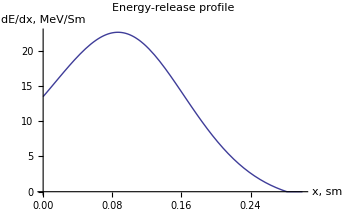

{22.6408,{y→0.0865334}}

```mathematica
Energy:=4;
A:=63.546;
Z:=29;
den:=8.92;

Ral:=0.421*Power[Energy,1.265-0.0954*Log[Energy]]/den;
Rp:=0.482*(A/Z)*Ral;
P[ksi_]=1.437/(({Cosh[0.95*(2.295*ksi-1)]}^1.8)*(0.5+1/(2.7-2.295*ksi)));
Q[x_]:=Energy/Rp P[x/Rp];

Plot[(Abs[Q[y]]+Q[y])/2,{y,0,0.3},AxesLabel->{"x, sm","dE/dx, MeV/Sm"},PlotLabel->"Energy-release profile"]
FindMaximum[(Abs[Q[y]]+Q[y])/2,{y,0}]
```

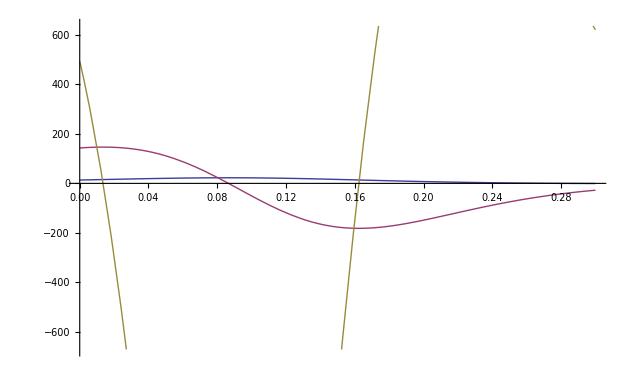

```mathematica
Rpw[En_]:=(63.546/29)*0.482*0.421*Power[En,1.265-0.0954*Log[En]]/8.92;
par[xv_,En_]:=xv/Rpw[En];
Pw[xv_,En_]=1.437/(({Cosh[0.95*(2.295*par[xv,En]-1)]}^1.8)*(0.5+1/(2.7-2.295*par[xv,En])));
Qw[xv_,En_]:=En/Rpw[En]*Pw[xv,En];
(*Plot3D[Qw[u,uu],{u,0,.3},{uu,3.9,4}]*)
(*Plot[Qw[u,4],{u,0,.3}];*)
dQw[xv_,En_]:=Derivative[1,0][Qw][xv,En]//Simplify;
d2Qw[xv_,En_]:=Derivative[2,0][Qw][xv,En]//Simplify;
Plot[{Qw[u,4],dQw[u,4],d2Qw[u,4]},{u,0,.3}]
```

```mathematica
ElementData[]
```

{Hydrogen,Helium,Lithium,Beryllium,Boron,Carbon,Nitrogen,Oxygen,Fluorine,Neon,Sodium,Magnesium,Aluminum,Silicon,Phosphorus,Sulfur,Chlorine,Argon,Potassium,Calcium,Scandium,Titanium,Vanadium,Chromium,Manganese,Iron,Cobalt,Nickel,Copper,Zinc,Gallium,Germanium,Arsenic,Selenium,Bromine,Krypton,Rubidium,Strontium,Yttrium,Zirconium,Niobium,Molybdenum,Technetium,Ruthenium,Rhodium,Palladium,Silver,Cadmium,Indium,Tin,Antimony,Tellurium,Iodine,Xenon,Cesium,Barium,Lanthanum,Cerium,Praseodymium,Neodymium,Promethium,Samarium,Europium,Gadolinium,Terbium,Dysprosium,Holmium,Erbium,Thulium,Ytterbium,Lutetium,Hafnium,Tantalum,Tungsten,Rhenium,Osmium,Iridium,Platinum,Gold,Mercury,Thallium,Lead,Bismuth,Polonium,Astatine,Radon,Francium,Radium,Actinium,Thorium,Protactinium,Uranium,Neptunium,Plutonium,Americium,Curium,Berkelium,Californium,Einsteinium,Fermium,Mendelevium,Nobelium,Lawrencium,Rutherfordium,Dubnium,Seaborgium,Bohrium,Hassium,Meitnerium,Darmstadtium,Roentgenium,Copernicium,Ununtrium,Ununquadium,Ununpentium,Ununhexium,Ununseptium,Ununoctium}

ALUMINIUM 1933 ALLOY

```mathematica
p2={{"Magnesium",1.6},{"Zinc",6.35},{"Copper",1},{"Manganese",.1},{"Iron",.2}, {"Silicon",.1},{"Titanium",.06},{"Chromium",.05},{"Zirconium",.1},{"Beryllium",.0001},{"Aluminum",90.44}};

SumPr=0;SumPz=0; SumPa=0;SumD=0;
dataT={};
AppendTo[dataT,{"Name","Z "," A","%","%*Z/100","%*A/100","Density*%/100"}];
For[i=1,i≤Length[p2],i++,{  
AppendTo[dataT,{p2[[i,1]],ElementData[p2[[i,1]],"AtomicNumber"],ElementData[p2[[i,1]],"AtomicWeight"],p2[[i,2]],.01*p2[[i,2]]*ElementData[p2[[i,1]],"AtomicNumber"],.01*p2[[i,2]]*ElementData[p2[[i,1]],"AtomicWeight"],.01*p2[[i,2]]*ElementData[p2[[i,1]],"Density"]}] ; 
SumPz=SumPz+dataT[[i+1,5]];
SumPa=SumPa+dataT[[i+1,6]];
SumD=SumD+dataT[[i+1,7]];
SumPr=SumPr+p2[[i,2]];
}];

AppendTo[dataT,{"","","Total Sum of %:: =",SumPr,"Average A::= ",SumPa,""}];
AppendTo[dataT,{"% Deviance::= ",100-SumPr,"","Average Z::= ",SumPz,"Average Density",SumD}];
Grid[dataT,Frame->True,Alignment->{Left},Background->{{{{Yellow,LightGreen}},{7->LightGray}},{{{LightRed,Pink}},{1->White}},{{-2,4}->Green,{-2,3}->Green,{-1,4}->Cyan,{-1,5}->Cyan,{-2,5}->Orange,{-2,6}->Orange,{-1,1}->LightPurple,{-1,2}->LightPurple,{-1,6}->LightGray,{-1,7}->LightGray}}]
```

Name | Z  |  A | % | %*Z/100 | %*A/100 | Density*%/100
Magnesium | 12 | 24.305 | 1.6 | 0.192 | 0.38888 | 27.808
Zinc | 30 | 65.38 | 6.35 | 1.905 | 4.15163 | 453.39
Copper | 29 | 63.546 | 1 | 0.29 | 0.63546 | 89.2
Manganese | 25 | 54.938045 | 0.1 | 0.025 | 0.054938 | 7.47
Iron | 26 | 55.845 | 0.2 | 0.052 | 0.11169 | 15.748
Silicon | 14 | 28.0855 | 0.1 | 0.014 | 0.0280855 | 2.33
Titanium | 22 | 47.867 | 0.06 | 0.0132 | 0.0287202 | 2.7042
Chromium | 24 | 51.9961 | 0.05 | 0.012 | 0.025998 | 3.57
Zirconium | 40 | 91.224 | 0.1 | 0.04 | 0.091224 | 6.511
Beryllium | 4 | 9.012182 | 0.0001 | 4.×10^-6 | 9.01218×10^-6 | 0.001848
Aluminum | 13 | 26.9815386 | 90.44 | 11.7572 | 24.4021 | 2441.88
 |  | Total Sum of %:: = | 100. | Average A::=  | 29.9187 | 
% Deviance::=  | -0.0001 |  | Average Z::=  | 14.3004 | Average Density | 3050.61

point coordinate at S_max::

```mathematica
Clear[Gh]; Clear[gg];

Gh=(29.918738317022/14.300403999999999)/2.853;
Rpq[En_]:=Gh*0.482*0.421*Power[En,1.265-0.0954*Log[En]];
pq[xv_,En_]:=xv/Rpq[En];
Pq[xv_,En_]=1.437/(({Cosh[0.95*(2.295*pq[xv,En]-1)]}^1.8)*(0.5+1/(2.7-2.295*pq[xv,En])));
Qq[xv_,En_]:=En/Rpq[En]*Pq[xv,En];
gg[en_]=0.07326 en^(1.265-0.0954 Log[en]) *Gh;
Manipulate[{mx:=FindArgMax[Qq[a,b],{a,0}]; Plot[Qq[a,b],{a,0,3.5*gg[b]},PlotRange->All],mx,gg[b],(gg[b]-mx),(gg[b]-mx)/mx},{b,0.02,4,.01}]
```

Plot::plln: Limiting value 3.5\ gg[3.16] in {a, 0, 3.5\ gg[FE`b$$1019]} is not a machine-sized real number.

FindArgMax::nrnum: The function value -3.33505/Gh is not a real number at {a} = {0.}.

General::stop: Further output of FindArgMax :: nrnum will be suppressed during this calculation.

Plot::plln: Limiting value 3.5\ gg[3.16] in {a, 0, 3.5\ gg[FE`b$$1019]} is not a machine-sized real number.

FindArgMax::nrnum: The function value -3.33505/Gh is not a real number at {a} = {0.}.

General::stop: Further output of FindArgMax :: nrnum will be suppressed during this calculation.

Plot::plln: Limiting value 3.5\ gg[3.16] in {a, 0, 3.5\ gg[FE`b$$1019]} is not a machine-sized real number.

FindArgMax::nrnum: The function value -3.33505/Gh is not a real number at {a} = {0.}.

General::stop: Further output of FindArgMax :: nrnum will be suppressed during this calculation.

Plot::plln: Limiting value 3.5\ gg[3.16] in {a, 0, 3.5\ gg[FE`b$$1019]} is not a machine-sized real number.

FindArgMax::nrnum: The function value -3.33505/Gh is not a real number at {a} = {0.}.

General::stop: Further output of FindArgMax :: nrnum will be suppressed during this calculation.

Plot::plln: Limiting value 3.5\ gg[3.16] in {a, 0, 3.5\ gg[FE`b$$1019]} is not a machine-sized real number.

FindArgMax::nrnum: The function value -3.33505/Gh is not a real number at {a} = {0.}.

General::stop: Further output of FindArgMax :: nrnum will be suppressed during this calculation.

Plot::plln: Limiting value 3.5\ gg[3.16] in {a, 0, 3.5\ gg[FE`b$$1019]} is not a machine-sized real number.

Plot::plln: Limiting value 3.5\ gg[3.16] in {a, 0, 3.5\ gg[FE`b$$49]} is not a machine-sized real number.

FindArgMax::nrnum: The function value -3.33505/Gh is not a real number at {a} = {0.}.

General::stop: Further output of FindArgMax :: nrnum will be suppressed during this calculation.

Plot::plln: Limiting value 3.5\ gg[3.16] in {a, 0, 3.5\ gg[FE`b$$49]} is not a machine-sized real number.

Plot::plln: Limiting value 3.5\ gg[3.16] in {a, 0, 3.5\ gg[FE`b$$16]} is not a machine-sized real number.

FindArgMax::nrnum: The function value -Qq[0., 3.16] is not a real number at {a} = {0.}.

General::stop: Further output of FindArgMax :: nrnum will be suppressed during this calculation.

Plot::plln: Limiting value 3.5\ gg[3.16] in {a, 0, 3.5\ gg[FE`b$$16]} is not a machine-sized real number.

General::stop: Further output of Plot :: plln will be suppressed during this calculation.

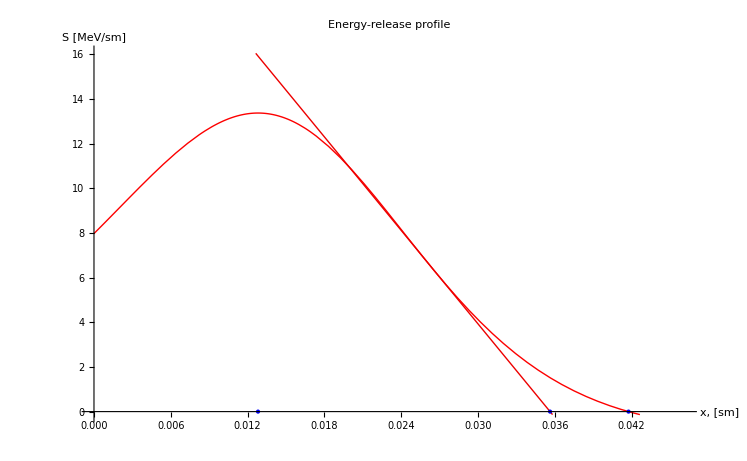

0.0128159

0.0417625

0.035633

```mathematica
Clear[Gh]; Clear[gg]; Clear[AtomicMass]; Clear[Charge]; Clear[MaterialDensity];
AtomicMass:=29.918738317022;Charge:=14.300403999999999; MaterialDensity:=2.853;
Gh=(AtomicMass/Charge)/MaterialDensity;
Rpq[En_]:=Gh*0.482*0.421*Power[En,1.265-0.0954*Log[En]];
pq[xv_,En_]:=xv/Rpq[En];
Pq[xv_,En_]=1.437/(({Cosh[0.95*(2.295*pq[xv,En]-1)]}^1.8)*(0.5+1/(2.7-2.295*pq[xv,En])));
Qq[xv_,En_]:=En/Rpq[En]*Pq[xv,En];
gg[en_]=0.073261 en^(1.265-0.0954 Log[en]) *Gh;
(*gn[en_]=(3.2586918469271406)*0.07326 en^(1.265-0.0954 Log[en]) *Gh//Simplify;*)
gn[en_]=Gh*0.23873176470588234 en^(1.265-0.0954 Log[en]);
(*gl[en_]=Gh*0.2396385 en^(1.265-0.0954 Log[en])*(0.85);*)
gl[en_]=Gh*0.203692725 en^(1.265-0.0954 Log[en]);
LL[xp_,en_]=InterpolatingPolynomial[{{gg[en]*1.55,Qq[gg[en]*1.55,en]},{gg[en]*2,Qq[gg[en]*2,en]}},xp];

eneg:=0.35;
Plot[{Qq[a,eneg],LL[a,eneg]},{a,0,3.5*gg[eneg]},PlotRange->{{0,3.6*gg[eneg]},{-0.01*FindMaxValue[Qq[x,eneg],{x,0,3.6*gg[eneg]}],1.2FindMaxValue[Qq[x,eneg],{x,0,3.6*gg[eneg]}]}},ColorFunction->Function[{x,y},If[y≥0,Red,Black]],ColorFunctionScaling->False,PlotStyle->Thick,Epilog->{PointSize[Large],Blue,Point[{gg[eneg],0}],Point[{gn[eneg],0}],Point[{gl[eneg],0}],

Text["density"MaterialDensity,{0.75,FindMaxValue[Qq[x,eneg],{x,0,3.5*gg[eneg]}]}],
Text["A"AtomicMass ,{0.75,0.9*FindMaxValue[Qq[x,eneg],{x,0,3.5*gg[eneg]}]}],
Text["Z"Charge,{0.75,.8*FindMaxValue[Qq[x,eneg],{x,0,3.5*gg[eneg]}]}]   },AxesLabel->{"x, [sm]","S [MeV/sm]"} ,PlotLabel->"Energy-release profile" ]
gg[eneg]
gn[eneg]
gl[eneg]

Clear[Gh]; Clear[gg]; Clear[AtomicMass]; Clear[Charge]; Clear[MaterialDensity]; ClearAll;
```

```mathematica
0.2396385 en^(1.265-0.0954 Log[en])*(0.85)//FullSimplify
```

0.203693 en^(1.265-0.0954 Log[en])

```mathematica
0.203692725/0.073261
```

2.78037

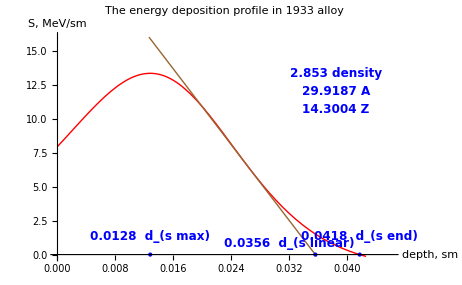

0.0128159

0.0417625

0.035633

```mathematica
Clear[Gh]; Clear[gg]; Clear[AtomicMass]; Clear[Charge]; Clear[MaterialDensity];
coef:=10000;
AtomicMass:=29.918738317022;Charge:=14.300403999999999; MaterialDensity:=2.853;
Gh=(AtomicMass/Charge)/MaterialDensity;
Rpq[En_]:=Gh*0.482*0.421*Power[En,1.265-0.0954*Log[En]];
pq[xv_,En_]:=xv/Rpq[En];
Pq[xv_,En_]=1.437/(({Cosh[0.95*(2.295*pq[xv,En]-1)]}^1.8)*(0.5+1/(2.7-2.295*pq[xv,En])));
Qq[xv_,En_]:=En/Rpq[En]*Pq[xv,En];
gg[en_]=0.073261 en^(1.265-0.0954 Log[en]) *Gh;
(*gn[en_]=(3.2586918469271406)*0.07326 en^(1.265-0.0954 Log[en]) *Gh//Simplify;*)
gn[en_]=Gh*0.23873176470588234 en^(1.265-0.0954 Log[en]);
(*gl[en_]=Gh*0.2396385 en^(1.265-0.0954 Log[en])*(0.85);*)
gl[en_]=Gh*0.203692725 en^(1.265-0.0954 Log[en]);
LL[xp_,en_]=InterpolatingPolynomial[{{gg[en]*1.55,Qq[gg[en]*1.55,en]},{gg[en]*2,Qq[gg[en]*2,en]}},xp];

eneg:=0.35;
Plot[{Qq[a,eneg],LL[a,eneg]},{a,0,3.5*gg[eneg]},PlotRange->{{0,3.6*gg[eneg]},{-0.01*FindMaxValue[Qq[x,eneg],{x,0,3.6*gg[eneg]}],1.2FindMaxValue[Qq[x,eneg],{x,0,3.6*gg[eneg]}]}},ColorFunctionScaling->False,PlotStyle->{{Red,Thick},{Brown,Thin}},AxesLabel->{"depth,  sm","S, MeV/sm"} ,AxesStyle->Directive[Black,12,Bold],PlotLabel->Style["The energy deposition profile in 1933 alloy",FontSize->16,Bold] ,Epilog->{PointSize[Large],Blue,Point[{gg[eneg],0}],Point[{gn[eneg],0}],Point[{gl[eneg],0}],

Text[Style["density"MaterialDensity,FontSize->12,Bold],{gg[eneg]*3,FindMaxValue[Qq[x,eneg],{x,0,3.5*gg[eneg]}]}],
Text[Style["A"AtomicMass ,FontSize->12,Bold],{gg[eneg]*3,0.9*FindMaxValue[Qq[x,eneg],{x,0,3.5*gg[eneg]}]}],
Text[Style["Z"Charge,FontSize->12,Bold],{gg[eneg]*3,.8*FindMaxValue[Qq[x,eneg],{x,0,3.5*gg[eneg]}]}],
Text[Style[" d_(s max)" NumberForm[gg[eneg],3],FontSize->12,Bold],{gg[eneg],0.1*FindMaxValue[Qq[x,eneg],{x,0,3.5*gg[eneg]}]}],
Text[Style[" d_(s linear)" NumberForm[gl[eneg],3],FontSize->12,Bold],{0.9*gl[eneg],0.06*FindMaxValue[Qq[x,eneg],{x,0,3.5*gg[eneg]}]}],
Text[Style[" d_(s end)"NumberForm[gn[eneg],3],FontSize->12,Bold],{1*gn[eneg],0.1*FindMaxValue[Qq[x,eneg],{x,0,3.5*gg[eneg]}]}]
  }]
gg[eneg]
gn[eneg]
gl[eneg]

Clear[Gh]; Clear[gg]; Clear[AtomicMass]; Clear[Charge]; Clear[MaterialDensity]; ClearAll;
```

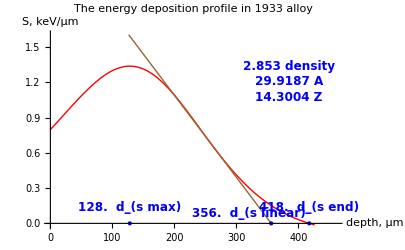

128.159

417.625

356.33

```mathematica
Clear[Gh]; Clear[gg]; Clear[AtomicMass]; Clear[Charge]; Clear[MaterialDensity];
coef:=10000;(*sm into microns*)
AtomicMass:=29.918738317022;Charge:=14.300403999999999; MaterialDensity:=2.853;
Gh=(AtomicMass/Charge)/MaterialDensity;
Rpq[En_]:=Gh*0.482*0.421*Power[En,1.265-0.0954*Log[En]];
pq[xv_,En_]:=xv/Rpq[En];
Pq[xv_,En_]=1.437/(({Cosh[0.95*(2.295*pq[xv,En]-1)]}^1.8)*(0.5+1/(2.7-2.295*pq[xv,En])));
Qq[xv_,En_]:=En/(Rpq[En]*10)*Pq[xv/coef,En];
gg[en_]=coef*0.073261 en^(1.265-0.0954 Log[en]) *Gh;
(*gn[en_]=(3.2586918469271406)*0.07326 en^(1.265-0.0954 Log[en]) *Gh//Simplify;*)
gn[en_]=coef*Gh*0.23873176470588234 en^(1.265-0.0954 Log[en]);
(*gl[en_]=Gh*0.2396385 en^(1.265-0.0954 Log[en])*(0.85);*)
gl[en_]=coef*Gh*0.203692725 en^(1.265-0.0954 Log[en]);
LL[xp_,en_]=InterpolatingPolynomial[{{gg[en]*1.55,Qq[gg[en]*1.55,en]},{gg[en]*2,Qq[gg[en]*2,en]}},xp];

eneg:=0.35;
Plot[{Qq[a,eneg],LL[a,eneg]},{a,0,3.5*gg[eneg]},PlotRange->{{0,3.6*gg[eneg]},{-0.01*FindMaxValue[Qq[x,eneg],{x,0,3.6*gg[eneg]}],1.2FindMaxValue[Qq[x,eneg],{x,0,3.6*gg[eneg]}]}},ColorFunctionScaling->False,PlotStyle->{{Red,Thick},{Brown,Thin}},AxesLabel->{"depth, μm","S, keV/μm"} ,AxesStyle->Directive[Black,12,Bold],PlotLabel->Style["The energy deposition profile in 1933 alloy",FontSize->16,Bold] ,Epilog->{PointSize[Large],Blue,Point[{gg[eneg],0}],Point[{gn[eneg],0}],Point[{gl[eneg],0}],

Text[Style["density"MaterialDensity,FontSize->12,Bold],{gg[eneg]*3,FindMaxValue[Qq[x,eneg],{x,0,3.5*gg[eneg]}]}],
Text[Style["A"AtomicMass ,FontSize->12,Bold],{gg[eneg]*3,0.9*FindMaxValue[Qq[x,eneg],{x,0,3.5*gg[eneg]}]}],
Text[Style["Z"Charge,FontSize->12,Bold],{gg[eneg]*3,.8*FindMaxValue[Qq[x,eneg],{x,0,3.5*gg[eneg]}]}],
Text[Style[" d_(s max)" NumberForm[gg[eneg],3],FontSize->12,Bold],{gg[eneg],0.1*FindMaxValue[Qq[x,eneg],{x,0,3.5*gg[eneg]}]}],
Text[Style[" d_(s linear)" NumberForm[gl[eneg],3],FontSize->12,Bold],{0.9*gl[eneg],0.06*FindMaxValue[Qq[x,eneg],{x,0,3.5*gg[eneg]}]}],
Text[Style[" d_(s end)"NumberForm[gn[eneg],3],FontSize->12,Bold],{1*gn[eneg],0.1*FindMaxValue[Qq[x,eneg],{x,0,3.5*gg[eneg]}]}]
  }]
gg[eneg]
gn[eneg]
gl[eneg]

Clear[Gh]; Clear[gg]; Clear[AtomicMass]; Clear[Charge]; Clear[MaterialDensity]; ClearAll;
```

```mathematica
α
```

```mathematica
μ
```